```mathematica
T[x_,t_]:=ArcTan[t-x]+ArcTan[t+x]
X[x_,t_]:=ArcTan[t+x]-ArcTan[t-x]
```

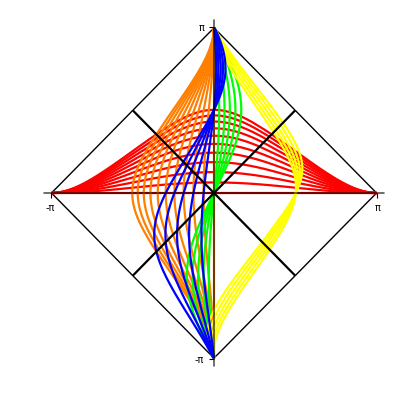

```mathematica
Poly=ParametricPlot[{{T[-50,t],X[-50,t]},{T[50,t],X[50,t]}},{t,-100,100},PlotRange->π,PlotPoints->1000,Axes->True,PlotStyle->{{Black,Thick},{Black,Thick}},Ticks->{{-π,π},{-π,π}}];
constantt=ParametricPlot[{{X[x,0],T[x,0]},{X[x,0.1],T[x,0.1]},{X[x,0.2],T[x,0.2]},{X[x,0.3],T[x,0.3]},{X[x,0.4],T[x,0.4]},{X[x,0.5],T[x,0.5]},{X[x,0.6],T[x,0.6]},{X[x,0.7],T[x,0.7]},{X[x,0.8],T[x,0.8]},{X[x,0.9],T[x,0.9]},{X[x,1],T[x,1]}},{x,-100,100},PlotRange->π,PlotPoints->1000,Axes->True,PlotStyle->{Red,Red,Red},Ticks->{{-π,π},{-π,π}}];
constantr=ParametricPlot[{{X[0,t],T[0,t]},{X[-0.1,t],T[-0.1,t]},{X[-0.2,t],T[-0.2,t]},{X[-0.3,t],T[-0.3,t]},{X[-0.4,t],T[-0.4,t]},{X[-0.5,t],T[-0.5,t]},{X[-0.6,t],T[-0.6,t]},{X[-0.7,t],T[-0.7,t]},{X[-0.8,t],T[-0.8,t]},{X[-0.9,t],T[-0.9,t]},{X[-1,t],T[-1,t]}},{t,-100,100},PlotRange->π,PlotPoints->1000,Axes->True,PlotStyle->{Orange,Orange,Orange},Ticks->{{-π,π},{-π,π}}];
timelikegeo=ParametricPlot[{{X[0.1t,t],T[0.1t,t]},{X[0.2t,t],T[0.2t,t]},{X[0.3t,t],T[0.3t,t]},{X[0.4t,t],T[0.4t,t]},{X[0.5t,t],T[0.5t,t]}},{t,-100,100},PlotRange->π,PlotPoints->1000,Axes->True,PlotStyle->{Green,Green,Green},Ticks->{{-π,π},{-π,π}}];
timelikegeo2=ParametricPlot[{{X[0.1t+1,t],T[0.1t+1,t]},{X[0.2t+1,t],T[0.2t+1,t]},{X[0.3t+1,t],T[0.3t+1,t]},{X[0.4t+1,t],T[0.4t+1,t]},{X[0.5t+1,t],T[0.5t+1,t]}},{t,-100,100},PlotRange->π,PlotPoints->1000,Axes->True,PlotStyle->{Yellow,Yellow,Yellow},Ticks->{{-π,π},{-π,π}}];
timelikegeo3=ParametricPlot[{{X[0.1t,t+1],T[0.1t,t+1]},{X[0.2t,t+1],T[0.2t,t+1]},{X[0.3t,t+1],T[0.3t,t+1]},{X[0.4t,t+1],T[0.4t,t+1]},{X[0.5t,t+1],T[0.5t,t+1]}},{t,-100,100},PlotRange->π,PlotPoints->1000,Axes->True,PlotStyle->{Blue,Blue,Blue},Ticks->{{-π,π},{-π,π}}];
lightcone=ParametricPlot[{{T[t+0,t],X[t+0,t]},{T[-t,t],X[-t,t]}},{t,-100,100},PlotRange->π,PlotPoints->1000,Axes->True,PlotStyle->{Black}];
Show[Poly,constantt,constantr,timelikegeo,timelikegeo2,timelikegeo3,lightcone]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
m=π;
M=π;
(*Outside horizon*)
tp[x_,t_]:=Sqrt[x/(2m)-1]Exp[x/(4m)]Sinh[t/(4m)]
xp[x_,t_]:=Sqrt[x/(2m)-1]Exp[x/(4m)]Cosh[t/(4m)]
u[x_,t_]:=(tp[x,t]-xp[x,t])
v[x_,t_]:=(tp[x,t]+xp[x,t])
U[x_,t_]:=ArcTan[u[x,t]]
V[x_,t_]:=ArcTan[v[x,t]]
X[x_,t_]:=V[x,t]-U[x,t]
T[x_,t_]:=V[x,t]+U[x,t]
(*Inside horizon*)
tpin[x_,t_]:=Sqrt[1-x/(2m)]Exp[x/(4m)]Cosh[t/(4m)]
xpin[x_,t_]:=Sqrt[1-x/(2m)]Exp[x/(4m)]Sinh[t/(4m)]
uin[x_,t_]:=(tpin[x,t]-xpin[x,t])
vin[x_,t_]:=(tpin[x,t]+xpin[x,t])
Uin[x_,t_]:=ArcTan[uin[x,t]]
Vin[x_,t_]:=ArcTan[vin[x,t]]
Xin[x_,t_]:=Vin[x,t]-Uin[x,t]
Tin[x_,t_]:=Vin[x,t]+Uin[x,t]
```

```mathematica
Sol1[s_]:=NDSolveValue[{y''[x]==(y'[x]^2-1)*2 M/(2*y[x]*(y[x]-2 M)),y[0]==0.1*M,y'[0]==0},y[s],{x,-Sinh[4],Sinh[4]}]
Sol2[s_]:=NDSolveValue[{y'[x]==-1/(1-2 M/Sol1[x]),y[0]==0},y[s],{x,-Sinh[4],Sinh[4]}]
```

```mathematica
Poly1=ParametricPlot[{{X[x,40],T[x,40]},{X[x,-40],T[x,-40]}},{x,-50,50},PlotRange->4,PlotPoints->5000,Axes->True,PlotStyle->{Black}];
S1=ParametricPlot[{{X[x,2],T[x,2]}},{x,-20,20},PlotRange->4,PlotPoints->1000,Axes->True,PlotStyle->{Blue}];
S2=ParametricPlot[{{Xin[Sol1[z],Sol2[z]],Tin[Sol1[z],Sol2[z]]}},{z,-6.5,6.5},PlotRange->π,PlotPoints->1000,Axes->True,PlotStyle->{Blue}]
```

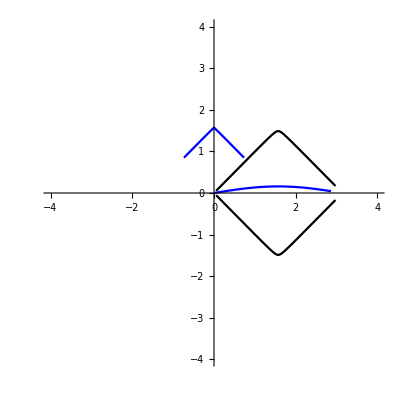

```mathematica
Show[Poly1,S1,S2]
```